# Animiranje grafov, vektorji in matrike

## Animiranje grafov

### Subsection. naloga:

Narišite graf funkcije y=a sin (k x+n) tako, da boste lahko vrednosti parametrov a, k in n spreminjali v obsegu od -3 do 3. Območje risanja omejite na [-5,5]×[-5,5]. Enoti na x in y osi naj bosta enako veliki.

```mathematica
(* V funkciji Plot uporabite nastavitvi Range->{-5,5} in AspectRatio->Automatic *)
Manipulate[Plot[a Sin[k x +n],{x,-5,5},PlotRange->{-5,5},AspectRatio->Automatic],{a,-3,3},{k,-3,3},{n,-3,3}]
```

### Subsection. naloga:

Narišite graf premice y=k x+n  in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0,y_0) tako, da boste lahko spreminjali vrednosti parametrov k, n, x_0 in y_0. Na sliki označite z majhnim krogcem, kje leži točka T.
Namig: dva grafa na isti sliki narišete s funkcijo Plot tako, da predpisa podate v seznamu: {f[x], g[x]}.

```mathematica
(* Točko dodate z nastavitvijo Epilog->{PointSize[Large],Point[{{x0,y0}}]}] *)
Manipulate[Plot[{k x+n,(x0-x)/k+y0},{x,-5,5}, PlotRange->{-5,5},AspectRatio->Automatic,Epilog->{PointSize[Large],Point[{{x0,y0}}]}],{k,-3,3},{n,-3,3},{y0,-3,3},{x0,-3,3}]
```

### Subsection. naloga:

Definirajte funkcijo  f(x)=(x(x-2))^2/(x^2+1) ter narišite njen graf skupaj s tangento v točki x_0, tako da boste lahko spreminjali vrednosti parametra x_0. Na sliki označite z majhnim krogcem, kje se tangenta dotika grafa funkcije.

```mathematica
f[x_]:=x(x-2)^2/(x^2+1)
Manipulate[Plot[{f[x],(D[f[t],t]/.t->x0)(x-x0)+f[x0]},{x,-5,5},PlotRange->{-10,3},AspectRatio->Automatic,Epilog->{PointSize[Large],Point[{{x0,f[x0]}}]}],{x0,-3,3}]
```

### Subsection. naloga:

1. Narišite graf implicitno podane funkcije  |x|^(2/3)+|y|^(2/3)=1  na območju [-1,1]×[-1,1]
2. Prikažite, kako se spreminja graf implicitne krivulje  |x|^p+|y|^p=1  za vrednosti parametra p∈[0,4]  z začetno vrednostjo 2.
3. Pri kateri vrednosti p leži točka (1/3,1/3) na grafu krivulje?

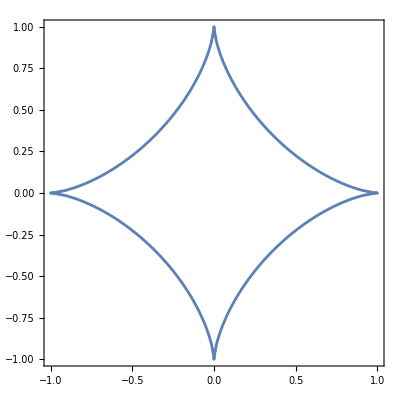

{{p→Log[2]/Log[3]}}

```mathematica
ContourPlot[Abs[x]^(2/3)+Abs[y]^(2/3)==1,{x,-1,1},{y,-1,1}]
Manipulate[ContourPlot[Abs[x]^p+Abs[y]^p==1,{x,-1,1},{y,-1,1}],{{p,2},0,4}]
Solve[Abs[x]^p+Abs[y]^p==1/.{x->1/3,y->1/3},p,Reals]
```

## Vektorji in matrike

### Subsection. naloga:

1. Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.
2. Izračunaj njun skalarni produkt.
3. Izračunaj njun vektorski produkt.s
4. Kateri od vektorjev je daljši?
5. Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

```mathematica
v1={1,2,3}
v2={-3,-2,5}
skalarniProdukt=v1.v2
vektorskiProdukt=Cross[v1,v2]
Norm[v1]<Norm[v2]

enotski=(vektorskiProdukt/Norm[vektorskiProdukt])
enotski.{x,y,z}==enotski.{1,1,1}//Simplify
```

{1,2,3}

{-3,-2,5}

8

{16,-14,4}

True

{8/(3 √13),-7/(3 √13),2/(3 √13)}

3+7 y==8 x+2 z

### Subsection. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3. S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

```mathematica
a={a1,a2,a3}
b={b1,b2,b3}
c={c1,c2,c3}
Cross[a,Cross[b,c]]==(a.c)b-(a.b)c//Simplify
```

{a1,a2,a3}

{b1,b2,b3}

{c1,c2,c3}

True

### Subsection. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.

```mathematica
a={{a11,a12},{a21,a22}}
b={{b11,b12},{b21,b22}}
Inverse[a.b]==Inverse[b].Inverse[a]//Simplify
```

{{a11,a12},{a21,a22}}

{{b11,b12},{b21,b22}}

True

### Subsection. naloga:

1. Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.
2. Izračunaj njeno determinanto.
3. Izračunaj njene lastne vrednosti.
4. Izračunaj njene lastne vektorje.
5. Ali je matrika diagonalizabilna?
6. Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.
7. Preveri, ali velja pogoj za diagonalizabilnost.

```mathematica
m={{9,2,-3},{3,2,1},{6,4,-1}}
m//MatrixForm
Det[m]
```

{{9,2,-3},{3,2,1},{6,4,-1}}

(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1)

-36

```mathematica
vrednosti=Eigenvalues[m]
```

{3 (1+√2),4,3 (1-√2)}

```mathematica
vektorji=Eigenvectors[m]//Simplify
```

{{1/6 (4+√2),1/(√2),1},{2,7,8},{1/6 (4-√2),-1/(√2),1}}

```mathematica
MatrixRank[m]==Length[m]
```

True

```mathematica
diag=DiagonalMatrix[vrednosti]
```

{{3 (1+√2),0,0},{0,4,0},{0,0,3 (1-√2)}}

```mathematica
preh=Transpose[vektorji]
```

{{1/6 (4+√2),2,1/6 (4-√2)},{1/(√2),7,-1/(√2)},{1,8,1}}

```mathematica
invPreh=Inverse[preh]//Simplify
```

{{3/34 (8+7 √2),1/17 (-4+5 √2),1/34 (1-14 √2)},{-3/17,1/17,2/17},{-3/34 (-8+7 √2),1/17 (-4-5 √2),1/34 (1+14 √2)}}

```mathematica
{diag//MatrixForm,preh//MatrixForm, invPreh//MatrixForm}
```

{(3 (1+√2) | 0 | 0
0 | 4 | 0
0 | 0 | 3 (1-√2)),(1/6 (4+√2) | 2 | 1/6 (4-√2)
1/(√2) | 7 | -1/(√2)
1 | 8 | 1),(3/34 (8+7 √2) | 1/17 (-4+5 √2) | 1/34 (1-14 √2)
-3/17 | 1/17 | 2/17
-3/34 (-8+7 √2) | 1/17 (-4-5 √2) | 1/34 (1+14 √2))}

```mathematica
invPreh.m.preh==diag
```

True